# PDE solver for effective field theory of Dark Energy

## Farbod Hassani and Jean-Pierre Eckmann

Feb 2021

In this note book we convert a PDE to coupled ODEs and we try to solve them in a cosmological settings.

## simple equation

```mathematica
Eq=Block[{pi},pi[t_,x_]:=assum[t,x];pde[t,x]]
```

pde[t,x]

```mathematica
For[i=1,i<6,i++,Print[ToString[x^i,StandardForm]<>": ",Coefficient[Eq,x^i]]]
```

x: 0

x^2: 0

x^3: 0

x^4: 0

x^5: 0

## Full PDE

In this section, I’m going to introduce xTensor, the main package of the xAct framework, and use it to demonstrate that the Lovelock tensor vanishes in four dimensions.

Load the package.

```mathematica
<<xAct`xTensor`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.0, {2013,1,27}

CopyRight (C) 2003-2013, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.0.5, {2013,1,30}

CopyRight (C) 2002-2013, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

This command specifies a manifold. I’ll call the manifold M4, and specify it has 4 dimensions. The indices associated with this manifold are a, b, c, etc.

```mathematica
DefManifold[M4,4,{a,b,c,d,e,f,g,h,i,j,k,l}]
```

** DefManifold: Defining manifold M4.

** DefVBundle: Defining vbundle TangentM4.

This command defines a metric. The first argument is the metric signature. The second argument is the name of the metric; note that it has to have two indices. The fact that there are minus signs indicates that the indices are lowered. CD is the name of the covariant derivative associated with the metric. Finally, I want Mathematica to print “metric” as “g”. Note that Mathematica knows that this metric is associated with M4 because of the indices that we use.

```mathematica
DefMetric[-1,metric[-a,-b],CD,PrintAs->"g"]
```

** DefTensor: Defining symmetric metric tensor metric[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilonmetric[-a,-b,-c,-d].

** DefTensor: Defining tensor Tetrametric[-a,-b,-c,-d].

** DefTensor: Defining tensor Tetrametric†[-a,-b,-c,-d].

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-a,-b].

** DefTensor: Defining Weyl tensor WeylCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining weight +2 density Detmetric[]. Determinant.

xTensor uses internal indices to manage things. This means that if I write down something with contracted indices, it will look like the following:

```mathematica
RicciScalarCD[]//RiemannToChristoffel
```

(g | l$994 | l$995
      |       (-Γ[▽] | l$1000 |       |      
       | l$997 | l$995 Γ[▽] | l$997 |       |       
      | l$994 | l$1000+Γ[▽] | l$1000 |       |      
       | l$994 | l$995 Γ[▽] | l$997 |       |       
      | l$997 | l$1000-∂_l$994 Γ[▽] | l$997 |       |      
      | l$997 | l$995+∂_l$997 Γ[▽] | l$997 |       |      
      | l$994 | l$995))

We specify the Mathematica $Pre variable, which controls printing, should fix these dollar indices appropriately.

```mathematica
$Pre=ScreenDollarIndices;
```

Then, hey presto:

```mathematica
RicciScalarCD[]//RiemannToChristoffel
```

(g | a | b
  |   (Γ[▽] | c |   |  
  | c | d Γ[▽] | d |   |  
  | a | b-Γ[▽] | c |   |  
  | a | d Γ[▽] | d |   |  
  | c | b-∂_a Γ[▽] | c |   |  
  | c | b+∂_c Γ[▽] | c |   |  
  | a | b))

Here is an expression that we are interested in:

```mathematica
Hold[RiemannCD[-a,-b,c,d] epsilonmetric[-i,-c,-d,-e] epsilonmetric[i,f,g,h]]
```

Hold[R[▽] |   |   | c | d
a | b |   |   ϵg |   |   |   |  
i | c | d | e ϵg | i | f | g | h
  |   |   |  ]

Note that if I release it, xTensor converts the epsilon products into Kronecker deltas as follows.

```mathematica
Release[%]
```

(δ |   | h
c |   δ |   | g
d |   δ |   | f
e |  -δ |   | g
c |   δ |   | h
d |   δ |   | f
e |  -δ |   | h
c |   δ |   | f
d |   δ |   | g
e |  +δ |   | f
c |   δ |   | h
d |   δ |   | g
e |  +δ |   | g
c |   δ |   | f
d |   δ |   | h
e |  -δ |   | f
c |   δ |   | g
d |   δ |   | h
e |  ) R[▽] |   |   | c | d
a | b |   |

The reason I’ve held it is that I want to antisymmetrize it, as follows. Note that we are antisymmetrizing over 5 indices in four dimensions: this thing is automatically zero.

```mathematica
Antisymmetrize[%%,{-a,-b,-c,-d,-e}]//Release
```

1/120 ((δ |   | h
b |   δ |   | g
c |   δ |   | f
e |  -δ |   | g
b |   δ |   | h
c |   δ |   | f
e |  -δ |   | h
b |   δ |   | f
c |   δ |   | g
e |  +δ |   | f
b |   δ |   | h
c |   δ |   | g
e |  +δ |   | g
b |   δ |   | f
c |   δ |   | h
e |  -δ |   | f
b |   δ |   | g
c |   δ |   | h
e |  ) g | c | l10
  |     R[▽] |   |    
a | l10+(δ |   | h
b |   δ |   | g
c |   δ |   | f
e |  -δ |   | g
b |   δ |   | h
c |   δ |   | f
e |  -δ |   | h
b |   δ |   | f
c |   δ |   | g
e |  +δ |   | f
b |   δ |   | h
c |   δ |   | g
e |  +δ |   | g
b |   δ |   | f
c |   δ |   | h
e |  -δ |   | f
b |   δ |   | g
c |   δ |   | h
e |  ) g | c | l12
  |     R[▽] |   |    
a | l12-(-δ |   | h
b |   δ |   | g
c |   δ |   | f
e |  +δ |   | g
b |   δ |   | h
c |   δ |   | f
e |  +δ |   | h
b |   δ |   | f
c |   δ |   | g
e |  -δ |   | f
b |   δ |   | h
c |   δ |   | g
e |  -δ |   | g
b |   δ |   | f
c |   δ |   | h
e |  +δ |   | f
b |   δ |   | g
c |   δ |   | h
e |  ) g | c | l14
  |     R[▽] |   |    
a | l14+«124»+3 (-δ |   | h
a |   δ |   | g
c |   δ |   | f
d |  +δ |   | g
a |   δ |   | h
c |   δ |   | f
d |  +δ |   | h
a |   δ |   | f
c |   δ |   | g
d |  -δ |   | f
a |   δ |   | h
c |   δ |   | g
d |  -δ |   | g
a |   δ |   | f
c |   δ |   | h
d |  +δ |   | f
a |   δ |   | g
c |   δ |   | h
d |  ) R[▽] |   |   | c | d
e | b |   |  )

Ok, that’s a little big. Let’s simplify by letting xTensor contract metrics where they appear.

```mathematica
result=%//ContractMetric
```

-1/5 δ |   | h
b |   δ |   | g
e |   R[▽] |   | f
a |  +1/5 δ |   | g
b |   δ |   | h
e |   R[▽] |   | f
a |  +1/5 δ |   | h
b |   δ |   | f
e |   R[▽] |   | g
a |  -1/5 δ |   | f
b |   δ |   | h
e |   R[▽] |   | g
a |  -1/5 δ |   | g
b |   δ |   | f
e |   R[▽] |   | h
a |  +1/5 δ |   | f
b |   δ |   | g
e |   R[▽] |   | h
a |  +1/5 δ |   | h
a |   δ |   | g
e |   R[▽] |   | f
b |  -1/5 δ |   | g
a |   δ |   | h
e |   R[▽] |   | f
b |  -1/5 δ |   | h
a |   δ |   | f
e |   R[▽] |   | g
b |  +1/5 δ |   | f
a |   δ |   | h
e |   R[▽] |   | g
b |  +1/5 δ |   | g
a |   δ |   | f
e |   R[▽] |   | h
b |  -1/5 δ |   | f
a |   δ |   | g
e |   R[▽] |   | h
b |  -1/5 δ |   | h
a |   δ |   | g
b |   R[▽] |   | f
e |  +1/5 δ |   | g
a |   δ |   | h
b |   R[▽] |   | f
e |  +1/5 δ |   | h
a |   δ |   | f
b |   R[▽] |   | g
e |  -1/5 δ |   | f
a |   δ |   | h
b |   R[▽] |   | g
e |  -1/5 δ |   | g
a |   δ |   | f
b |   R[▽] |   | h
e |  +1/5 δ |   | f
a |   δ |   | g
b |   R[▽] |   | h
e |  +1/10 δ |   | h
a |   δ |   | g
b |   δ |   | f
e |   R[▽]-1/10 δ |   | g
a |   δ |   | h
b |   δ |   | f
e |   R[▽]-1/10 δ |   | h
a |   δ |   | f
b |   δ |   | g
e |   R[▽]+1/10 δ |   | f
a |   δ |   | h
b |   δ |   | g
e |   R[▽]+1/10 δ |   | g
a |   δ |   | f
b |   δ |   | h
e |   R[▽]-1/10 δ |   | f
a |   δ |   | g
b |   δ |   | h
e |   R[▽]-1/20 δ |   | h
e |   R[▽] |   |   | f | g
a | b |   |  +1/20 δ |   | g
e |   R[▽] |   |   | f | h
a | b |   |  +1/20 δ |   | h
e |   R[▽] |   |   | g | f
a | b |   |  -1/20 δ |   | f
e |   R[▽] |   |   | g | h
a | b |   |  -1/20 δ |   | g
e |   R[▽] |   |   | h | f
a | b |   |  +1/20 δ |   | f
e |   R[▽] |   |   | h | g
a | b |   |  +1/20 δ |   | h
b |   R[▽] |   |   | f | g
a | e |   |  -1/20 δ |   | g
b |   R[▽] |   |   | f | h
a | e |   |  -1/20 δ |   | h
b |   R[▽] |   |   | g | f
a | e |   |  +1/20 δ |   | f
b |   R[▽] |   |   | g | h
a | e |   |  +1/20 δ |   | g
b |   R[▽] |   |   | h | f
a | e |   |  -1/20 δ |   | f
b |   R[▽] |   |   | h | g
a | e |   |  +1/20 δ |   | h
e |   R[▽] |   |   | f | g
b | a |   |  -1/20 δ |   | g
e |   R[▽] |   |   | f | h
b | a |   |  -1/20 δ |   | h
e |   R[▽] |   |   | g | f
b | a |   |  +1/20 δ |   | f
e |   R[▽] |   |   | g | h
b | a |   |  +1/20 δ |   | g
e |   R[▽] |   |   | h | f
b | a |   |  -1/20 δ |   | f
e |   R[▽] |   |   | h | g
b | a |   |  -1/20 δ |   | h
a |   R[▽] |   |   | f | g
b | e |   |  +1/20 δ |   | g
a |   R[▽] |   |   | f | h
b | e |   |  +1/20 δ |   | h
a |   R[▽] |   |   | g | f
b | e |   |  -1/20 δ |   | f
a |   R[▽] |   |   | g | h
b | e |   |  -1/20 δ |   | g
a |   R[▽] |   |   | h | f
b | e |   |  +1/20 δ |   | f
a |   R[▽] |   |   | h | g
b | e |   |  -1/20 δ |   | h
b |   R[▽] |   |   | f | g
e | a |   |  +1/20 δ |   | g
b |   R[▽] |   |   | f | h
e | a |   |  +1/20 δ |   | h
b |   R[▽] |   |   | g | f
e | a |   |  -1/20 δ |   | f
b |   R[▽] |   |   | g | h
e | a |   |  -1/20 δ |   | g
b |   R[▽] |   |   | h | f
e | a |   |  +1/20 δ |   | f
b |   R[▽] |   |   | h | g
e | a |   |  +1/20 δ |   | h
a |   R[▽] |   |   | f | g
e | b |   |  -1/20 δ |   | g
a |   R[▽] |   |   | f | h
e | b |   |  -1/20 δ |   | h
a |   R[▽] |   |   | g | f
e | b |   |  +1/20 δ |   | f
a |   R[▽] |   |   | g | h
e | b |   |  +1/20 δ |   | g
a |   R[▽] |   |   | h | f
e | b |   |  -1/20 δ |   | f
a |   R[▽] |   |   | h | g
e | b |   |

That’s still pretty big. But note that we have some degeneracies here. These degeneracies look like the following:

```mathematica
RiemannCD[-a,-b,c,d]+RiemannCD[-b,-a,d,c]
```

R[▽] |   |   | c | d
a | b |   |  +R[▽] |   |   | d | c
b | a |   |

Note that RiemannCD is the Riemann tensor from the metric with covariant derivative CD. We can ask xTensor to canonicalize this expression, by using whatever symmetries are available to it to simplify things. The command to do this is ToCanonical, and is easily the most complicated command in xTensor, under the hood. Thankfully, it’s also a really easy command to use. It will fix the above as

```mathematica
%//ToCanonical
```

2 R[▽] |   |   | c | d
a | b |   |

Because of the funny internal storage of indices, it will also fix expressions like the following:

```mathematica
CD[-a][CD[a][RicciScalarCD[]]]+CD[-b]@CD[b]@RicciScalarCD[]
%//ToCanonical
```

▽_a▽^a R[▽]+▽_b▽^b R[▽]

2 (▽_a▽^a R[▽])

Note that this demonstrates two ways to write covariant derivatives. The @ command is a Mathematica shorthand (see howto/UseShorthandNotations in the help).

Let’s go back and canonicalize our expression. Remember that this is exactly zero in four dimensions.

```mathematica
result//ToCanonical
```

-1/5 δ |   | h
b |   δ |   | g
e |   R[▽] |   | f
a |  +1/5 δ |   | g
b |   δ |   | h
e |   R[▽] |   | f
a |  +1/5 δ |   | h
b |   δ |   | f
e |   R[▽] |   | g
a |  -1/5 δ |   | f
b |   δ |   | h
e |   R[▽] |   | g
a |  -1/5 δ |   | g
b |   δ |   | f
e |   R[▽] |   | h
a |  +1/5 δ |   | f
b |   δ |   | g
e |   R[▽] |   | h
a |  +1/5 δ |   | h
a |   δ |   | g
e |   R[▽] |   | f
b |  -1/5 δ |   | g
a |   δ |   | h
e |   R[▽] |   | f
b |  -1/5 δ |   | h
a |   δ |   | f
e |   R[▽] |   | g
b |  +1/5 δ |   | f
a |   δ |   | h
e |   R[▽] |   | g
b |  +1/5 δ |   | g
a |   δ |   | f
e |   R[▽] |   | h
b |  -1/5 δ |   | f
a |   δ |   | g
e |   R[▽] |   | h
b |  -1/5 δ |   | h
a |   δ |   | g
b |   R[▽] |   | f
e |  +1/5 δ |   | g
a |   δ |   | h
b |   R[▽] |   | f
e |  +1/5 δ |   | h
a |   δ |   | f
b |   R[▽] |   | g
e |  -1/5 δ |   | f
a |   δ |   | h
b |   R[▽] |   | g
e |  -1/5 δ |   | g
a |   δ |   | f
b |   R[▽] |   | h
e |  +1/5 δ |   | f
a |   δ |   | g
b |   R[▽] |   | h
e |  +1/10 δ |   | h
a |   δ |   | g
b |   δ |   | f
e |   R[▽]-1/10 δ |   | g
a |   δ |   | h
b |   δ |   | f
e |   R[▽]-1/10 δ |   | h
a |   δ |   | f
b |   δ |   | g
e |   R[▽]+1/10 δ |   | f
a |   δ |   | h
b |   δ |   | g
e |   R[▽]+1/10 δ |   | g
a |   δ |   | f
b |   δ |   | h
e |   R[▽]-1/10 δ |   | f
a |   δ |   | g
b |   δ |   | h
e |   R[▽]-1/5 δ |   | h
e |   R[▽] |   |   | f | g
a | b |   |  +1/5 δ |   | g
e |   R[▽] |   |   | f | h
a | b |   |  -1/5 δ |   | f
e |   R[▽] |   |   | g | h
a | b |   |  +1/5 δ |   | h
b |   R[▽] |   |   | f | g
a | e |   |  -1/5 δ |   | g
b |   R[▽] |   |   | f | h
a | e |   |  +1/5 δ |   | f
b |   R[▽] |   |   | g | h
a | e |   |  -1/5 δ |   | h
a |   R[▽] |   |   | f | g
b | e |   |  +1/5 δ |   | g
a |   R[▽] |   |   | f | h
b | e |   |  -1/5 δ |   | f
a |   R[▽] |   |   | g | h
b | e |   |

Now I’m going to multiply this by some stuff, and do a little bit of cleaning up.

```mathematica
5 /2metric[-h,-l] RiemannCD[-f,-g,e,a] %//Expand//ContractMetric//ToCanonical//Simplify
```

1/2 (-8 R[▽] |   | a
b |   R[▽] |   |  
l | a+4 R[▽] |   |  
b | l R[▽]+g |   |  
b | l (4 R[▽] |   |  
a | e R[▽] | a | e
  |  -R[▽]^2-R[▽] |   |   |   |  
a | e | f | g R[▽] | a | e | f | g
  |   |   |  )-8 R[▽] | a | e
  |   R[▽] |   |   |   |  
b | a | l | e+4 R[▽] |   | a | e | f
b |   |   |   R[▽] |   |   |   |  
l | a | e | f)

I’d like to write this in a bit nicer notation by collecting all the metric components together.

```mathematica
IndexCollect[Expand@%,metric[-b,-l]]
```

-4 R[▽] |   | a
b |   R[▽] |   |  
l | a+2 R[▽] |   |  
b | l R[▽]+g |   |  
b | l (2 R[▽] |   |  
a | c R[▽] | a | c
  |  -R[▽]^2/2-1/2 R[▽] |   |   |   |  
a | c | d | e R[▽] | a | c | d | e
  |   |   |  )-4 R[▽] | a | e
  |   R[▽] |   |   |   |  
b | a | l | e+2 R[▽] |   | a | e | f
b |   |   |   R[▽] |   |   |   |  
l | a | e | f

This is the Lovelock tensor. What we’ve just done is the simplest way to show that it’s zero in four dimensions. This is also the expression that we get if we vary an action containing the Gauss-Bonnet term. Actually seeing that it’s zero from that perspective is really quite difficult, however. Regardless, all of these manipulations took mere seconds. Doing this expansion by hand takes a decent amount of time.

Because all of the manipulations done here are essentially manipulating integers and nothing else, all of these results are incredible reliable, so long as you don’t make a mistake in the process of typing it in!

```mathematica
Clear[result]
```

## Obtaining the ODEs

```mathematica
Eq=Block[{pi},pi[t_,x_]:=assum[t,x];pde[t,x]]
```

-4 x^2 a[t]^2+x^2 a''[t]

```mathematica
For[i=1,i<6,i++,Print[ToString[x^i,StandardForm]<>": ",Coefficient[Eq,x^i]]]
```

x: 0

x^2: -4 a[t]^2+a''[t]

x^3: 0

x^4: 0

x^5: 0

```mathematica
Solvind the full equation for k-essence π^(..) +Lin=NL
```

```mathematica
Clear[Eq,assum,pde];
```

#### PDE and assumptions

```mathematica
Ψ[τ_,x_]:=ψ0[τ] +ψ1[τ] x + ψ2[τ] x^2 +ψ3[τ] x^3+ ψ4[τ] x^4;
assum[t_,x_] := Subscript[u, 0][t]+ Subscript[u, 1][t]x +  Subscript[u, 2][t] x^2+Subscript[u, 3][t] x^3+Subscript[u, 4][t] x^4;
L[τ_,x_] := Subscript[l, πd][τ]D[pi[τ,x], τ] + Subscript[l, ππ][τ]pi[τ,x]+Subscript[l, Ψ][τ] Ψ[τ,x]+Subscript[l, Ψd][τ] D[Ψ[τ,x], τ]+Subscript[l, πpp][τ]D[pi[τ,x], x,x];
NonLin[τ_,x_]:= Subscript[ν, πpπp][τ] (D[pi[τ,x], x])^2 +Subscript[ν, πpπpd][τ]D[pi[τ,x], x]D[pi[τ,x], τ,x] + Subscript[ν, ππpp][τ] pi[τ,x]D[pi[τ,x], x,x]
+Subscript[ν, πdπpp][τ] D[pi[τ,x], τ] D[pi[τ,x], x,x]+Subscript[ν, Ψπpp][τ] Ψ[τ,x] D[pi[τ,x], x,x]+Subscript[ν, Ψpπp][τ] D[Ψ[τ,x], x]D[pi[τ,x], x]+Subscript[ν, πpπpπpp][τ](D[pi[τ,x], x])^2 D[pi[τ,x], x,x];
```

#### Print the equation

```mathematica
Print[L[τ,x]//pdConv]
```

l_πpp(τ) (∂^2 pi(τ,x))/(∂x^2)+l_πd(τ) (∂pi(τ,x))/(∂τ)+l_ππ(τ) pi(τ,x)+x^3 ψ0(τ) ψ1(τ) ψ2(τ) l_Ψ(τ) (x^4 ψ4(τ)+x^3 ψ3(τ))+l_Ψd(τ) (x^3 ψ0(τ) ψ1(τ) ψ2(τ) (x^4 (∂ψ4(τ))/(∂τ)+x^3 (∂ψ3(τ))/(∂τ))+x^3 ψ0(τ) ψ1(τ) (∂ψ2(τ))/(∂τ) (x^4 ψ4(τ)+x^3 ψ3(τ))+x^3 ψ0(τ) ψ2(τ) (∂ψ1(τ))/(∂τ) (x^4 ψ4(τ)+x^3 ψ3(τ))+x^3 ψ1(τ) ψ2(τ) (∂ψ0(τ))/(∂τ) (x^4 ψ4(τ)+x^3 ψ3(τ)))

```mathematica
(*Printing non-linear terms and checked *)
```

```mathematica
Print[NonLin[τ,x]//pdConv];
```

pdConv[(ψ1[τ]+2 x ψ2[τ]+3 x^2 ψ3[τ]+4 x^3 ψ4[τ]) ν_Ψpπp[τ] pi^(0,1)[τ,x]+ν_πpπp[τ] (pi^(0,1)[τ,x])^2+pi[τ,x] ν_ππpp[τ] pi^(0,2)[τ,x]+(ψ0[τ]+x ψ1[τ]+x^2 ψ2[τ]+x^3 ψ3[τ]+x^4 ψ4[τ]) ν_Ψπpp[τ] pi^(0,2)[τ,x]+ν_πpπpπpp[τ] (pi^(0,1)[τ,x])^2 pi^(0,2)[τ,x]+ν_πdπpp[τ] pi^(0,2)[τ,x] pi^(1,0)[τ,x]+ν_πpπpd[τ] pi^(0,1)[τ,x] pi^(1,1)[τ,x]]

```mathematica
The full equation without linear terms
```

equation full linear terms The without

```mathematica
Eq[t_,x_]:= D[pi[t,x], t,t]+1*L[t,x]-NonLin[t,x];
```

```mathematica
Print[Eq[τ,x]//pdConv];
```

-ν_πpπpd(τ) (∂pi(τ,x))/(∂x) (∂^2 pi(τ,x))/(∂τ ∂x)+l_πpp(τ) (∂^2 pi(τ,x))/(∂x^2)+l_πd(τ) (∂pi(τ,x))/(∂τ)+l_ππ(τ) pi(τ,x)-ν_πdπpp(τ) (∂pi(τ,x))/(∂τ) (∂^2 pi(τ,x))/(∂x^2)-ν_ππpp(τ) pi(τ,x) (∂^2 pi(τ,x))/(∂x^2)-ν_πpπpπpp(τ) (∂^2 pi(τ,x))/(∂x^2) ((∂pi(τ,x))/(∂x))^2-ν_Ψpπp(τ) (∂pi(τ,x))/(∂x) (ψ1(τ)+4 x^3 ψ4(τ)+3 x^2 ψ3(τ)+2 x ψ2(τ))-ν_Ψπpp(τ) (∂^2 pi(τ,x))/(∂x^2) (ψ0(τ)+x^4 ψ4(τ)+x^3 ψ3(τ)+x^2 ψ2(τ)+x ψ1(τ))-ν_πpπp(τ) ((∂pi(τ,x))/(∂x))^2+(∂^2 pi(τ,x))/(∂τ^2)+l_Ψ(τ) (ψ0(τ)+x^4 ψ4(τ)+x^3 ψ3(τ)+x^2 ψ2(τ)+x ψ1(τ))+l_Ψd(τ) ((∂ψ0(τ))/(∂τ)+x^4 (∂ψ4(τ))/(∂τ)+x^3 (∂ψ3(τ))/(∂τ)+x^2 (∂ψ2(τ))/(∂τ)+x (∂ψ1(τ))/(∂τ))

```mathematica
NewEq=Block[{pi},pi[τ_,x_]:=Subscript[u, 0][τ]+ Subscript[u, 1][τ]x +  Subscript[u, 2][τ] x^2+Subscript[u, 3][τ] x^3+Subscript[u, 4][τ] x^4;Eq[τ,x]]
```

(ψ0[τ]+x ψ1[τ]+x^2 ψ2[τ]+x^3 ψ3[τ]+x^4 ψ4[τ]) l_Ψ[τ]+l_πpp[τ] (2 u_2[τ]+6 x u_3[τ]+12 x^2 u_4[τ])+l_ππ[τ] (u_0[τ]+x u_1[τ]+x^2 u_2[τ]+x^3 u_3[τ]+x^4 u_4[τ])-(u_1[τ]+2 x u_2[τ]+3 x^2 u_3[τ]+4 x^3 u_4[τ])^2 ν_πpπp[τ]-(2 u_2[τ]+6 x u_3[τ]+12 x^2 u_4[τ]) (u_1[τ]+2 x u_2[τ]+3 x^2 u_3[τ]+4 x^3 u_4[τ])^2 ν_πpπpπpp[τ]-(2 u_2[τ]+6 x u_3[τ]+12 x^2 u_4[τ]) (u_0[τ]+x u_1[τ]+x^2 u_2[τ]+x^3 u_3[τ]+x^4 u_4[τ]) ν_ππpp[τ]-(ψ1[τ]+2 x ψ2[τ]+3 x^2 ψ3[τ]+4 x^3 ψ4[τ]) (u_1[τ]+2 x u_2[τ]+3 x^2 u_3[τ]+4 x^3 u_4[τ]) ν_Ψpπp[τ]-(ψ0[τ]+x ψ1[τ]+x^2 ψ2[τ]+x^3 ψ3[τ]+x^4 ψ4[τ]) (2 u_2[τ]+6 x u_3[τ]+12 x^2 u_4[τ]) ν_Ψπpp[τ]+l_Ψd[τ] (ψ0'[τ]+x ψ1'[τ]+x^2 ψ2'[τ]+x^3 ψ3'[τ]+x^4 ψ4'[τ])-(u_1[τ]+2 x u_2[τ]+3 x^2 u_3[τ]+4 x^3 u_4[τ]) ν_πpπpd[τ] (u_1'[τ]+2 x u_2'[τ]+3 x^2 u_3'[τ]+4 x^3 u_4'[τ])+l_πd[τ] (u_0'[τ]+x u_1'[τ]+x^2 u_2'[τ]+x^3 u_3'[τ]+x^4 u_4'[τ])-(2 u_2[τ]+6 x u_3[τ]+12 x^2 u_4[τ]) ν_πdπpp[τ] (u_0'[τ]+x u_1'[τ]+x^2 u_2'[τ]+x^3 u_3'[τ]+x^4 u_4'[τ])+u_0''[τ]+x u_1''[τ]+x^2 u_2''[τ]+x^3 u_3''[τ]+x^4 u_4''[τ]

```mathematica
For[i=0,i<5,i++,If[i==0, Print["x^0:"NewEq /.{x->0}]];If[i!=0,Print[ToString[x^i,StandardForm]<>": ",Coefficient[NewEq,x^i]]]]
```

x^0: (ψ0[τ] l_Ψ[τ]+l_ππ[τ] u_0[τ]+2 l_πpp[τ] u_2[τ]-u_1[τ]^2 ν_πpπp[τ]-2 u_1[τ]^2 u_2[τ] ν_πpπpπpp[τ]-2 u_0[τ] u_2[τ] ν_ππpp[τ]-ψ1[τ] u_1[τ] ν_Ψpπp[τ]-2 ψ0[τ] u_2[τ] ν_Ψπpp[τ]+l_Ψd[τ] ψ0'[τ]+l_πd[τ] u_0'[τ]-2 u_2[τ] ν_πdπpp[τ] u_0'[τ]-u_1[τ] ν_πpπpd[τ] u_1'[τ]+u_0''[τ])

x: ψ1[τ] l_Ψ[τ]+l_ππ[τ] u_1[τ]+6 l_πpp[τ] u_3[τ]-4 u_1[τ] u_2[τ] ν_πpπp[τ]-8 u_1[τ] u_2[τ]^2 ν_πpπpπpp[τ]-6 u_1[τ]^2 u_3[τ] ν_πpπpπpp[τ]-2 u_1[τ] u_2[τ] ν_ππpp[τ]-6 u_0[τ] u_3[τ] ν_ππpp[τ]-2 ψ2[τ] u_1[τ] ν_Ψpπp[τ]-2 ψ1[τ] u_2[τ] ν_Ψpπp[τ]-2 ψ1[τ] u_2[τ] ν_Ψπpp[τ]-6 ψ0[τ] u_3[τ] ν_Ψπpp[τ]+l_Ψd[τ] ψ1'[τ]-6 u_3[τ] ν_πdπpp[τ] u_0'[τ]+l_πd[τ] u_1'[τ]-2 u_2[τ] ν_πdπpp[τ] u_1'[τ]-2 u_2[τ] ν_πpπpd[τ] u_1'[τ]-2 u_1[τ] ν_πpπpd[τ] u_2'[τ]+u_1''[τ]

x^2: ψ2[τ] l_Ψ[τ]+l_ππ[τ] u_2[τ]+12 l_πpp[τ] u_4[τ]-4 u_2[τ]^2 ν_πpπp[τ]-6 u_1[τ] u_3[τ] ν_πpπp[τ]-8 u_2[τ]^3 ν_πpπpπpp[τ]-36 u_1[τ] u_2[τ] u_3[τ] ν_πpπpπpp[τ]-12 u_1[τ]^2 u_4[τ] ν_πpπpπpp[τ]-2 u_2[τ]^2 ν_ππpp[τ]-6 u_1[τ] u_3[τ] ν_ππpp[τ]-12 u_0[τ] u_4[τ] ν_ππpp[τ]-3 ψ3[τ] u_1[τ] ν_Ψpπp[τ]-4 ψ2[τ] u_2[τ] ν_Ψpπp[τ]-3 ψ1[τ] u_3[τ] ν_Ψpπp[τ]-2 ψ2[τ] u_2[τ] ν_Ψπpp[τ]-6 ψ1[τ] u_3[τ] ν_Ψπpp[τ]-12 ψ0[τ] u_4[τ] ν_Ψπpp[τ]+l_Ψd[τ] ψ2'[τ]-12 u_4[τ] ν_πdπpp[τ] u_0'[τ]-6 u_3[τ] ν_πdπpp[τ] u_1'[τ]-3 u_3[τ] ν_πpπpd[τ] u_1'[τ]+l_πd[τ] u_2'[τ]-2 u_2[τ] ν_πdπpp[τ] u_2'[τ]-4 u_2[τ] ν_πpπpd[τ] u_2'[τ]-3 u_1[τ] ν_πpπpd[τ] u_3'[τ]+u_2''[τ]

x^3: ψ3[τ] l_Ψ[τ]+l_ππ[τ] u_3[τ]-12 u_2[τ] u_3[τ] ν_πpπp[τ]-8 u_1[τ] u_4[τ] ν_πpπp[τ]-48 u_2[τ]^2 u_3[τ] ν_πpπpπpp[τ]-36 u_1[τ] u_3[τ]^2 ν_πpπpπpp[τ]-64 u_1[τ] u_2[τ] u_4[τ] ν_πpπpπpp[τ]-8 u_2[τ] u_3[τ] ν_ππpp[τ]-12 u_1[τ] u_4[τ] ν_ππpp[τ]-4 ψ4[τ] u_1[τ] ν_Ψpπp[τ]-6 ψ3[τ] u_2[τ] ν_Ψpπp[τ]-6 ψ2[τ] u_3[τ] ν_Ψpπp[τ]-4 ψ1[τ] u_4[τ] ν_Ψpπp[τ]-2 ψ3[τ] u_2[τ] ν_Ψπpp[τ]-6 ψ2[τ] u_3[τ] ν_Ψπpp[τ]-12 ψ1[τ] u_4[τ] ν_Ψπpp[τ]+l_Ψd[τ] ψ3'[τ]-12 u_4[τ] ν_πdπpp[τ] u_1'[τ]-4 u_4[τ] ν_πpπpd[τ] u_1'[τ]-6 u_3[τ] ν_πdπpp[τ] u_2'[τ]-6 u_3[τ] ν_πpπpd[τ] u_2'[τ]+l_πd[τ] u_3'[τ]-2 u_2[τ] ν_πdπpp[τ] u_3'[τ]-6 u_2[τ] ν_πpπpd[τ] u_3'[τ]-4 u_1[τ] ν_πpπpd[τ] u_4'[τ]+u_3''[τ]

x^4: ψ4[τ] l_Ψ[τ]+l_ππ[τ] u_4[τ]-9 u_3[τ]^2 ν_πpπp[τ]-16 u_2[τ] u_4[τ] ν_πpπp[τ]-90 u_2[τ] u_3[τ]^2 ν_πpπpπpp[τ]-80 u_2[τ]^2 u_4[τ] ν_πpπpπpp[τ]-120 u_1[τ] u_3[τ] u_4[τ] ν_πpπpπpp[τ]-6 u_3[τ]^2 ν_ππpp[τ]-14 u_2[τ] u_4[τ] ν_ππpp[τ]-8 ψ4[τ] u_2[τ] ν_Ψpπp[τ]-9 ψ3[τ] u_3[τ] ν_Ψpπp[τ]-8 ψ2[τ] u_4[τ] ν_Ψpπp[τ]-2 ψ4[τ] u_2[τ] ν_Ψπpp[τ]-6 ψ3[τ] u_3[τ] ν_Ψπpp[τ]-12 ψ2[τ] u_4[τ] ν_Ψπpp[τ]+l_Ψd[τ] ψ4'[τ]-12 u_4[τ] ν_πdπpp[τ] u_2'[τ]-8 u_4[τ] ν_πpπpd[τ] u_2'[τ]-6 u_3[τ] ν_πdπpp[τ] u_3'[τ]-9 u_3[τ] ν_πpπpd[τ] u_3'[τ]+l_πd[τ] u_4'[τ]-2 u_2[τ] ν_πdπpp[τ] u_4'[τ]-8 u_2[τ] ν_πpπpd[τ] u_4'[τ]+u_4''[τ]

```mathematica
Cosmology functions:
```

```mathematica
(*scale factor in terms of the Redshift  *)
scalfactor[z_]:=1/(1+z);
redshift[a_]:=1/a-1;
```

```mathematica
(*Function to compute conformal time for a given redshift*)
tau[zs_,H0_,Ωm_,Ωd_,w_,Ωr_]:=NIntegrate[H0^-1/(√(Ωd(1+z)^(3(1+w)) +Ωm (1+z)^3+Ωr(1+z)^4)),{z,zs,∞},PrecisionGoal->12,AccuracyGoal->12]
```

```mathematica
(*Function to compute Physical time for a given redshift = (a'(tau))/a*)
time[zs_,H0_,Ωm_,Ωd_,w_,Ωr_]:=NIntegrate[H0^-1/((1+z)√(Ωd(1+z)^(3(1+w)) +Ωm (1+z)^3+Ωr(1+z)^4)),{z,zs,∞}]
```

```mathematica
(*Physical Hubble Function at a given redshift = (ȧ)/a *)
PhysicalHubble[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=H0 √(Ωd(1+z)^(3(1+w)) +Ωm (1+z)^3+Ωr(1+z)^4)
```

```mathematica
(*Conformal Hubble Function at a given redshift *)
ConformalHubble[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=H0 √(Ωd(1+z)^(1+3 w) +Ωm (1+z)+Ωr(1+z)^2)
```

```mathematica
(*Conformal Hubble Function at a given redshift *)
ConformalHubble[τ_,H0_,Ωm_,Ωd_,w_,Ωr_]:=H0 √(Ωd(1+z)^(1+3 w) +Ωm (1+z)+Ωr(1+z)^2)
```

```mathematica
(*Time derivative of the Conformal Hubble Function at a given redshift = (ȧ)/a *)
ConformalHubblePrime[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=D[ConformalHubble[z,H0,Ωm,Ωd,w,Ωr],z]*(-(1+z)^2)*ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]*1/(1+z);  (* (d HH)/dtau = dH/dz  dz/da da/dtau*)
```

# Cosmological settings

```mathematica
w = -0.7;
cs2=10^-8;
H0=0.0691023;
Ωm=0.31;
Ωr=9 10^-5;
Ωd=1-Ωm-Ωr;
```

```mathematica
Solving the coupled ODEs:
```

```mathematica
Linear coeficients definition:
```

```mathematica
Subscript[l, πd][τ] = (1-3 w) Η[τ,H0,Ωm,Ωd,w,Ωr];
Subscript[l, ππ][τ] = (1-3cs2) Ηprime[τ,H0,Ωm,Ωd,w,Ωr] + 3(cs2-w) Η[τ,H0,Ωm,Ωd,w,Ωr]^2;
Subscript[l, Ψ][τ] = 3(w-cs2) Η[τ,H0,Ωm,Ωd,w,Ωr];
Subscript[l, Ψd][τ] = -(1+3cs2);
Subscript[l, πpp][τ] = -cs2;
```

```mathematica
Non-linear coeficients definition:
```

```mathematica
Subscript[ν, πpπp][τ]  = (-Η[τ,H0,Ωm,Ωd,w,Ωr])/2 (5 cs2 +3 w -2);
Subscript[ν, πpπpd][τ] = 2(1-cs2);
Subscript[ν, ππpp][τ] = -Η[τ,H0,Ωm,Ωd,w,Ωr]( (cs2-1) + 3 cs2(1+w));
Subscript[ν, πdπpp][τ] = -(cs2-1);
Subscript[ν, Ψπpp][τ] = (cs2-1);
Subscript[ν, Ψpπp][τ] = (cs2-1);
Subscript[ν, πpπpπpp][τ] = 3/2(cs2-1);
```

Set of equations

```mathematica
Psiequation[ψ_,τ_,Ωm_,Ωd_,w_,Ωr_]:= ψ''[τ] + 3 Η[τ,H0,Ωm,Ωd,w,Ωr]ψ'[τ]+((2-(3 Ωm)/(2 Ωm + 2 Ωd a[τ]^(-3 w)+ 2 Ωr a[τ]^-1))Η[τ,H0,Ωm,Ωd,w,Ωr]^2+ Ηprime[τ,H0,Ωm,Ωd,w,Ωr])ψ[τ];

Eqψ0 = ψ0''[τ] + 3 Η[τ,H0,Ωm,Ωd,w,Ωr]ψ0'[τ]+((2-(3 Ωm)/(2 Ωm + 2 Ωd a[τ]^(-3 w)+ 2 Ωr a[τ]^-1))Η[τ,H0,Ωm,Ωd,w,Ωr]^2+ Ηprime[τ,H0,Ωm,Ωd,w,Ωr])ψ0[τ];
Eqψ1 = ψ1''[τ] + 3 Η[τ,H0,Ωm,Ωd,w,Ωr]ψ1'[τ]+((2-(3 Ωm)/(2 Ωm + 2 Ωd a[τ]^(-3 w)+ 2 Ωr a[τ]^-1))Η[τ,H0,Ωm,Ωd,w,Ωr]^2+ Ηprime[τ,H0,Ωm,Ωd,w,Ωr])ψ1[τ];
Eqψ2 = ψ2''[τ] + 3 Η[τ,H0,Ωm,Ωd,w,Ωr]ψ2'[τ]+((2-(3 Ωm)/(2 Ωm + 2 Ωd a[τ]^(-3 w)+ 2 Ωr a[τ]^-1))Η[τ,H0,Ωm,Ωd,w,Ωr]^2+ Ηprime[τ,H0,Ωm,Ωd,w,Ωr])ψ2[τ];
Eqψ3 = ψ3''[τ] + 3 Η[τ,H0,Ωm,Ωd,w,Ωr]ψ3'[τ]+((2-(3 Ωm)/(2 Ωm + 2 Ωd a[τ]^(-3 w)+ 2 Ωr a[τ]^-1))Η[τ,H0,Ωm,Ωd,w,Ωr]^2+ Ηprime[τ,H0,Ωm,Ωd,w,Ωr])ψ3[τ];
Eqψ4 = ψ4''[τ] + 3 Η[τ,H0,Ωm,Ωd,w,Ωr]ψ4'[τ]+((2-(3 Ωm)/(2 Ωm + 2 Ωd a[τ]^(-3 w)+ 2 Ωr a[τ]^-1))Η[τ,H0,Ωm,Ωd,w,Ωr]^2+ Ηprime[τ,H0,Ωm,Ωd,w,Ωr])ψ4[τ];
eqn0=NewEq/.{x->0};
eqn1=Coefficient[NewEq,x^1];
eqn2=Coefficient[NewEq,x^2];
eqn3=Coefficient[NewEq,x^3];
eqn4=Coefficient[NewEq,x^4];
```

## Assumptions

```mathematica
assumptions = {Η[τ,H0,Ωm,Ωd,w,Ωr]->2/τ,Ηprime[τ,H0,Ωm,Ωd,w,Ωr]->-2/τ^2, ψ0[τ]->0,ψ1[τ]->0,ψ2[τ]->10^-4,ψ3[τ]->0,ψ4[τ]->0, ψ0'[τ]->0,ψ1'[τ]->0,ψ2'[τ]->0,ψ3'[τ]->0,ψ4'[τ]->0};
(*ψ0[τ]:=0
ψ1[τ]:=0
ψ2[τ]:=10^-5
ψ3[τ]:=0
ψ4[τ]:=0*)
eqn0 = eqn0/.assumptions;
eqn1 = eqn1/.assumptions;
eqn2 = eqn2/.assumptions;
eqn3 = eqn3/.assumptions;
eqn4 = eqn4/.assumptions;
```

```mathematica
τini = tau[1000,H0,Ωm,Ωd,w,Ωr];
τfin = tau[0,H0,Ωm,Ωd,w,Ωr];

s=NDSolve[{eqn0==0,eqn1==0, eqn2==0, eqn3==0, eqn4==0,Subscript[u, 0][τini]==0.0,Subscript[u, 0]'[τini]==0.0,Subscript[u, 1][τini]==0.,
Subscript[u, 1]'[τini]==0.0,Subscript[u, 2][τini]==0.0,Subscript[u, 2]'[τini]==0,Subscript[u, 3][τini]==0.,Subscript[u, 3]'[τini]==0.0,Subscript[u, 4][τini]==0.0,
Subscript[u, 4]'[τini]==0.0},{Subscript[u, 0][t],Subscript[u, 0]'[τ],Subscript[u, 1][τ],Subscript[u, 1]'[τ],Subscript[u, 2][τ],Subscript[u, 2]'[τ],Subscript[u, 3][τ],Subscript[u, 3]'[τ],Subscript[u, 4][τ],Subscript[u, 4]'[τ]},{τ,τini,τfin}]
```

{{u_0[t]→InterpolatingFunction[…][t],u_0'[τ]→InterpolatingFunction[…][τ],u_1[τ]→InterpolatingFunction[…][τ],u_1'[τ]→InterpolatingFunction[…][τ],u_2[τ]→InterpolatingFunction[…][τ],u_2'[τ]→InterpolatingFunction[…][τ],u_3[τ]→InterpolatingFunction[…][τ],u_3'[τ]→InterpolatingFunction[…][τ],u_4[τ]→InterpolatingFunction[…][τ],u_4'[τ]→InterpolatingFunction[…][τ]}}

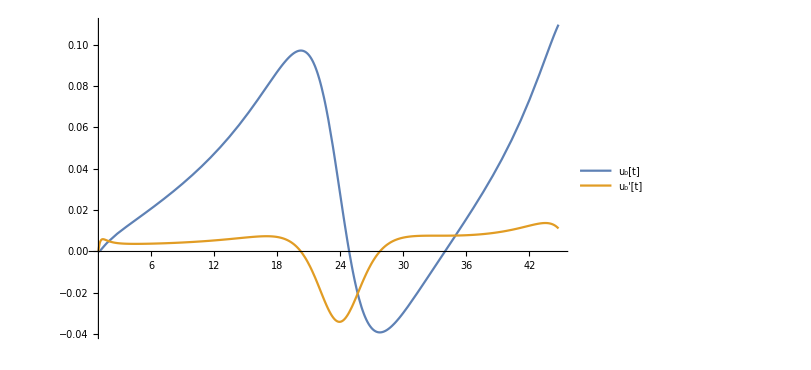

```mathematica
plt = Plot[Evaluate[{Subscript[u, 2][τ],Subscript[u, 2]'[τ]}/.s],{τ,τini,τfin},PlotRange->Full,PlotLegends->{"u_0[t]","u_0'[t]"}, PlotStyle->Thick, ImageSize->600]
```

```mathematica
{Subscript[u, 2][τ],Subscript[u, 2]'[τ]}/.s/.τ->43.00
```

{{-0.0590856,-0.000270185}}

```mathematica
τini = tau[1000,H0,Ωm,Ωd,w,Ωr]
τfin = tau[0,H0,Ωm,Ωd,w,Ωr]
```

0.980812

43.0056